```mathematica
path = ".";
```

```mathematica
l = Import[path<>"mouse-segregation-1.ods"];
```

```mathematica
sheet = Take[l[[1]], {3, 19}]
```

{{,,JF1-C57,RR-C57,HB_C57,ST_C57,BG_C57,LE_C57,NZW_C57,NZB_BALB,NZB_129S6,,,JF1-C57,RR-C57,HB_C57,ST_C57,BG_C57,LE_C57,NZW_C57,NZB_BALB,NZB_129S6,},{1,Gut,,1,-1,1,1,1,-1,,,,,,1,4,1,0,0,5,,,},{2,Spleen,,-1,1,1,1,1,-1,2,2,,,,3,2,1,0,0,5,1,1,},{3,Skin,,,-1,1,1,-1,-1,,,,,,,4,1,0,5,5,,,},{4,Uterus,,,-1,1,1,-1,,,,,,,,4,1,0,5,,,,},{5,Blood,,,1,1,1,-1,,2,,,,,,2,1,0,5,,1,,},{6,Pancreas,,,,,,,,,2,,,,,,,,,,,1,},{7,Ovary,,1,,,,,,,2,,,,1,,,,,,,1,},{7.5,Stomach,,1,,,,,-1,,,,,,1,,,,,5,,,},{8,Liver,1,1,1,1,-1,1,-1,1,1,,,1,1,2,1,5,0,5,1,1,},{9,Kidney,-1,1,-1,1,-1,1,-1,1,1,,,3,1,4,1,5,0,5,1,1,},{10,Testis,,,-1,1,1,-1,,,,,,,,4,1,0,5,,,,},{11,Tail,-1,,-1,1,1,-1,,-1,1,,,3,,4,1,0,5,,3,1,},{12,Lung,,,1,1,-1,1,-1,-1,,,,,,2,1,5,0,5,3,,},{13,Muscle,,,2,1,-1,-1,-1,-1,2,,,,,2,1,5,5,5,3,0,},{14,Brain,2,2,-1,-1,-1,-1,-1,-1,1,,,1,1,4,3,5,5,5,3,1,},{15,Heart,,2,2,-1,-1,-1,-1,-1,-1,,,,1,2,3,5,5,5,3,3,}}

```mathematica
nnames = 9;
ntissues = 16;
```

```mathematica
names = Table[sheet[[1]][[i]], {i, 3, 3+nnames-1}]
tissues = Table[sheet[[i]][[2]], {i, 2, 2+ntissues-1}]
```

{JF1-C57,RR-C57,HB_C57,ST_C57,BG_C57,LE_C57,NZW_C57,NZB_BALB,NZB_129S6}

{Gut,Spleen,Skin,Uterus,Blood,Pancreas,Ovary,Stomach,Liver,Kidney,Testis,Tail,Lung,Muscle,Brain,Heart}

```mathematica
data = Transpose[Table[ Table[sheet[[i]][[j]],{j,3, 3+nnames-1}], {i, 2, 2+ntissues-1}]]
```

{{,,,,,,,,1,-1,,-1,,,2,},{1,-1,,,,,1,1,1,1,,,,,2,2},{-1,1,-1,-1,1,,,,1,-1,-1,-1,1,2,-1,2},{1,1,1,1,1,,,,1,1,1,1,1,1,-1,-1},{1,1,1,1,1,,,,-1,-1,1,1,-1,-1,-1,-1},{1,1,-1,-1,-1,,,,1,1,-1,-1,1,-1,-1,-1},{-1,-1,-1,,,,,-1,-1,-1,,,-1,-1,-1,-1},{,2,,,2,,,,1,1,,-1,-1,-1,-1,-1},{,2,,,,2,2,,1,1,,1,,2,1,-1}}

```mathematica
m = 0.7;
```

```mathematica
Pos[x_,y_] := {RGBColor[1, m,m], Disk[{x,y},0.4],Red, Text["+", {x, y}]};
Neg[x_,y_] := {RGBColor[m,m, 1], Disk[{x,y},0.4],Blue, Text["-", {x, y}]};
Neut[x_,y_] := {RGBColor[0.9, 0.9, 0.9], Disk[{x,y},0.4],Gray, Text["0", {x, y}]};
Miss[x_,y_] := {LightGray, Text["X", {x, y}]};
Ques[x_,y_] := {Black, Text["?", {x, y}]};
```

```mathematica
points=Table[Table[Switch[data[[i]][[j]], 1, Pos[i,-j],2,Neg[i,-j], -1, Neut[i,-j], "", Miss[i,-j], 2, Ques[i,-j]], {j, 1, Length[data[[1]]]}], {i, 1, Length[data]}];
```

```mathematica
collabels = Table[{Text[names[[i]], {i, 0.}, {-1,0}, {0,1}]}, {i, 1, Length[names]}];
```

```mathematica
rowlabels = Table[Text[tissues[[i]], {-0.0, -i}, {1, 0}],{i, 1, Length[tissues]}];
```

```mathematica
end = Length[data]+1;
```

```mathematica
braces1 = Line[{{end,-1}, {end+0.2, -1}, {end+0.2, -8}, {end, -8}}];
braces2 = Line[{{end,-9}, {end+0.2, -9}, {end+0.2, -12}, {end, -12}}];
braces3 = Line[{{end,-13}, {end+0.2, -13}, {end+0.2, -16}, {end, -16}}];
```

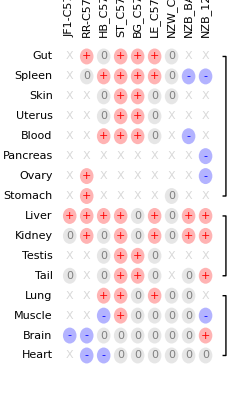

```mathematica
set = Graphics[{points, collabels, rowlabels, braces1, braces2, braces3}]
```

```mathematica
Export[path<>"present-mouse-tissues.svg", set]
```